```mathematica
SetDirectory["C:\\Users\\Mason\\Desktop\\VoltageRelaxation\\"];
Data=Import["er1.csv"];
ListPlot3D[Data,PlotRange->All]
SetDirectory["C:\\Users\\Mason\\Desktop\\VoltageRelaxation\\"];
Data2=Import["er4.csv"];
ListPlot3D[Data2,PlotRange->All]
SetDirectory["C:\\Users\\Mason\\Desktop\\VoltageRelaxation\\"];
Data3=Import["er1000.csv"];
ListPlot3D[Data3,PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Data1=Import["Efield1.csv"];
ListVectorPlot[Data1]
Data1=Import["Efield4.csv"];
ListVectorPlot[Data1]
Data1=Import["Efield1000.csv"];
ListVectorPlot[Data1]
```

$Aborted

$Aborted

Visualization`Core`ListVectorPlot::vfldata: {{100.,0.},{52.7377,0.},{36.0386,0.},{30.2029,0.},{28.3282,0.},«42»,{2.08465,-6.27066},{0.00621302,-0.00773173},{0.00664866,-0.000499979},«31»} is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot[{{100.,0.},{52.7377,0.},{36.0386,0.},{30.2029,0.},{28.3282,0.},{28.328,0.},{30.2025,0.},{36.0382,0.},{52.7374,0.},{0.,-47.2623},{22.1742,-16.6991},{25.1746,-5.83574},{26.2411,-1.87475},{26.4526,-0.000146149},{26.4525,1.87451},{26.2406,5.83567},{25.1742,16.6992},{22.1739,47.2626},{0.,-25.088},{10.7843,-13.6987},{16.2441,-4.76932},{23.1333,-1.66316},{24.7882,-0.000309079},{24.788,1.66263},{23.1326,4.76923},{16.2437,13.699},{10.784,25.0887},{0.,-14.3038},{4.7185,-8.23884},{5.88383,2.11984},{0.0252412,-0.00828492},{0.0254527,-0.000499979},{0.0254526,0.00728526},{0.0252411,-2.11975},{5.88369,8.23934},{4.71838,14.3047},{0.,-9.58526},{2.20584,-7.07351},{2.54745,-3.73875},{0.0155379,-0.00807345},{0.0158796,-0.000500033},{0.0158797,0.00707371},{0.0155381,3.7387},{2.54745,7.07403},{2.20584,9.58628},{0.,-7.37942},{1.55745,-6.7319},{2.08465,-6.27066},{0.00621302,-0.00773173},{0.00664866,-0.000499979},{0.00664882,0.0067321},{0.00621348,6.27062},{2.08479,6.73242},{1.55756,7.38044},{0.,-5.82197},{1.93942,-6.20469},{4.22769,-8.3491},{8.84486,-0.00729609},{7.75087,-0.000499816},{7.75106,0.00629675},{8.84551,8.3492},{4.22817,6.20519},{1.9397,5.82288},{0.,-3.88255},{1.97283,-3.91642},{4.04247,-3.73194},{6.21333,-1.10128},{6.64898,-0.000308911},{6.64915,1.10075},{6.21378,3.73185},{4.04295,3.91672},{1.97315,3.88318},{0.,-1.90972},{1.90972,-1.84679},{3.7565,-1.56108},{5.31758,-0.665627},{5.98321,-0.000146038},{5.98336,0.665386},{5.31797,1.56102},{3.75695,1.84692},{1.91003,1.91003}}]

```mathematica
Data3==Data2
```

True

1

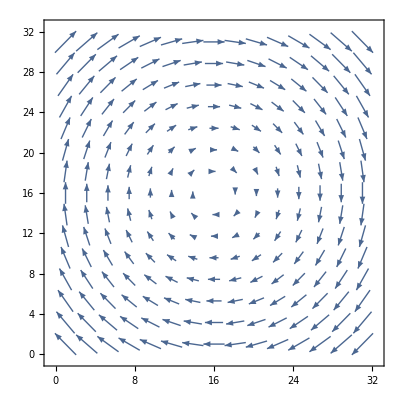

```mathematica
(i)-(i-1)
```

```mathematica
a=Table[{y,-x},{x,-3,3,0.2},{y,-3,3,0.2}];
Save["C:\\Users\\Mason\\Desktop\\VoltageRelaxation\\funky.csv",a]
```

```mathematica
a
```

{{{-3.,3.},{-2.8,3.},{-2.6,3.},{-2.4,3.},{-2.2,3.},{-2.,3.},{-1.8,3.},{-1.6,3.},{-1.4,3.},{-1.2,3.},{-1.,3.},{-0.8,3.},{-0.6,3.},{-0.4,3.},{-0.2,3.},{0.,3.},{0.2,3.},{0.4,3.},{0.6,3.},{0.8,3.},{1.,3.},{1.2,3.},{1.4,3.},{1.6,3.},{1.8,3.},{2.,3.},{2.2,3.},{2.4,3.},{2.6,3.},{2.8,3.},{3.,3.}},{{-3.,2.8},{-2.8,2.8},{-2.6,2.8},{-2.4,2.8},{-2.2,2.8},{-2.,2.8},{-1.8,2.8},{-1.6,2.8},{-1.4,2.8},{-1.2,2.8},{-1.,2.8},{-0.8,2.8},{-0.6,2.8},{-0.4,2.8},{-0.2,2.8},{0.,2.8},{0.2,2.8},{0.4,2.8},{0.6,2.8},{0.8,2.8},{1.,2.8},{1.2,2.8},{1.4,2.8},{1.6,2.8},{1.8,2.8},{2.,2.8},{2.2,2.8},{2.4,2.8},{2.6,2.8},{2.8,2.8},{3.,2.8}},{{-3.,2.6},{-2.8,2.6},{-2.6,2.6},{-2.4,2.6},{-2.2,2.6},{-2.,2.6},{-1.8,2.6},{-1.6,2.6},{-1.4,2.6},{-1.2,2.6},{-1.,2.6},{-0.8,2.6},{-0.6,2.6},{-0.4,2.6},{-0.2,2.6},{0.,2.6},{0.2,2.6},{0.4,2.6},{0.6,2.6},{0.8,2.6},{1.,2.6},{1.2,2.6},{1.4,2.6},{1.6,2.6},{1.8,2.6},{2.,2.6},{2.2,2.6},{2.4,2.6},{2.6,2.6},{2.8,2.6},{3.,2.6}},{{-3.,2.4},{-2.8,2.4},{-2.6,2.4},{-2.4,2.4},{-2.2,2.4},{-2.,2.4},{-1.8,2.4},{-1.6,2.4},{-1.4,2.4},{-1.2,2.4},{-1.,2.4},{-0.8,2.4},{-0.6,2.4},{-0.4,2.4},{-0.2,2.4},{0.,2.4},{0.2,2.4},{0.4,2.4},{0.6,2.4},{0.8,2.4},{1.,2.4},{1.2,2.4},{1.4,2.4},{1.6,2.4},{1.8,2.4},{2.,2.4},{2.2,2.4},{2.4,2.4},{2.6,2.4},{2.8,2.4},{3.,2.4}},{{-3.,2.2},{-2.8,2.2},{-2.6,2.2},{-2.4,2.2},{-2.2,2.2},{-2.,2.2},{-1.8,2.2},{-1.6,2.2},{-1.4,2.2},{-1.2,2.2},{-1.,2.2},{-0.8,2.2},{-0.6,2.2},{-0.4,2.2},{-0.2,2.2},{0.,2.2},{0.2,2.2},{0.4,2.2},{0.6,2.2},{0.8,2.2},{1.,2.2},{1.2,2.2},{1.4,2.2},{1.6,2.2},{1.8,2.2},{2.,2.2},{2.2,2.2},{2.4,2.2},{2.6,2.2},{2.8,2.2},{3.,2.2}},{{-3.,2.},{-2.8,2.},{-2.6,2.},{-2.4,2.},{-2.2,2.},{-2.,2.},{-1.8,2.},{-1.6,2.},{-1.4,2.},{-1.2,2.},{-1.,2.},{-0.8,2.},{-0.6,2.},{-0.4,2.},{-0.2,2.},{0.,2.},{0.2,2.},{0.4,2.},{0.6,2.},{0.8,2.},{1.,2.},{1.2,2.},{1.4,2.},{1.6,2.},{1.8,2.},{2.,2.},{2.2,2.},{2.4,2.},{2.6,2.},{2.8,2.},{3.,2.}},{{-3.,1.8},{-2.8,1.8},{-2.6,1.8},{-2.4,1.8},{-2.2,1.8},{-2.,1.8},{-1.8,1.8},{-1.6,1.8},{-1.4,1.8},{-1.2,1.8},{-1.,1.8},{-0.8,1.8},{-0.6,1.8},{-0.4,1.8},{-0.2,1.8},{0.,1.8},{0.2,1.8},{0.4,1.8},{0.6,1.8},{0.8,1.8},{1.,1.8},{1.2,1.8},{1.4,1.8},{1.6,1.8},{1.8,1.8},{2.,1.8},{2.2,1.8},{2.4,1.8},{2.6,1.8},{2.8,1.8},{3.,1.8}},{{-3.,1.6},{-2.8,1.6},{-2.6,1.6},{-2.4,1.6},{-2.2,1.6},{-2.,1.6},{-1.8,1.6},{-1.6,1.6},{-1.4,1.6},{-1.2,1.6},{-1.,1.6},{-0.8,1.6},{-0.6,1.6},{-0.4,1.6},{-0.2,1.6},{0.,1.6},{0.2,1.6},{0.4,1.6},{0.6,1.6},{0.8,1.6},{1.,1.6},{1.2,1.6},{1.4,1.6},{1.6,1.6},{1.8,1.6},{2.,1.6},{2.2,1.6},{2.4,1.6},{2.6,1.6},{2.8,1.6},{3.,1.6}},{{-3.,1.4},{-2.8,1.4},{-2.6,1.4},{-2.4,1.4},{-2.2,1.4},{-2.,1.4},{-1.8,1.4},{-1.6,1.4},{-1.4,1.4},{-1.2,1.4},{-1.,1.4},{-0.8,1.4},{-0.6,1.4},{-0.4,1.4},{-0.2,1.4},{0.,1.4},{0.2,1.4},{0.4,1.4},{0.6,1.4},{0.8,1.4},{1.,1.4},{1.2,1.4},{1.4,1.4},{1.6,1.4},{1.8,1.4},{2.,1.4},{2.2,1.4},{2.4,1.4},{2.6,1.4},{2.8,1.4},{3.,1.4}},{{-3.,1.2},{-2.8,1.2},{-2.6,1.2},{-2.4,1.2},{-2.2,1.2},{-2.,1.2},{-1.8,1.2},{-1.6,1.2},{-1.4,1.2},{-1.2,1.2},{-1.,1.2},{-0.8,1.2},{-0.6,1.2},{-0.4,1.2},{-0.2,1.2},{0.,1.2},{0.2,1.2},{0.4,1.2},{0.6,1.2},{0.8,1.2},{1.,1.2},{1.2,1.2},{1.4,1.2},{1.6,1.2},{1.8,1.2},{2.,1.2},{2.2,1.2},{2.4,1.2},{2.6,1.2},{2.8,1.2},{3.,1.2}},{{-3.,1.},{-2.8,1.},{-2.6,1.},{-2.4,1.},{-2.2,1.},{-2.,1.},{-1.8,1.},{-1.6,1.},{-1.4,1.},{-1.2,1.},{-1.,1.},{-0.8,1.},{-0.6,1.},{-0.4,1.},{-0.2,1.},{0.,1.},{0.2,1.},{0.4,1.},{0.6,1.},{0.8,1.},{1.,1.},{1.2,1.},{1.4,1.},{1.6,1.},{1.8,1.},{2.,1.},{2.2,1.},{2.4,1.},{2.6,1.},{2.8,1.},{3.,1.}},{{-3.,0.8},{-2.8,0.8},{-2.6,0.8},{-2.4,0.8},{-2.2,0.8},{-2.,0.8},{-1.8,0.8},{-1.6,0.8},{-1.4,0.8},{-1.2,0.8},{-1.,0.8},{-0.8,0.8},{-0.6,0.8},{-0.4,0.8},{-0.2,0.8},{0.,0.8},{0.2,0.8},{0.4,0.8},{0.6,0.8},{0.8,0.8},{1.,0.8},{1.2,0.8},{1.4,0.8},{1.6,0.8},{1.8,0.8},{2.,0.8},{2.2,0.8},{2.4,0.8},{2.6,0.8},{2.8,0.8},{3.,0.8}},{{-3.,0.6},{-2.8,0.6},{-2.6,0.6},{-2.4,0.6},{-2.2,0.6},{-2.,0.6},{-1.8,0.6},{-1.6,0.6},{-1.4,0.6},{-1.2,0.6},{-1.,0.6},{-0.8,0.6},{-0.6,0.6},{-0.4,0.6},{-0.2,0.6},{0.,0.6},{0.2,0.6},{0.4,0.6},{0.6,0.6},{0.8,0.6},{1.,0.6},{1.2,0.6},{1.4,0.6},{1.6,0.6},{1.8,0.6},{2.,0.6},{2.2,0.6},{2.4,0.6},{2.6,0.6},{2.8,0.6},{3.,0.6}},{{-3.,0.4},{-2.8,0.4},{-2.6,0.4},{-2.4,0.4},{-2.2,0.4},{-2.,0.4},{-1.8,0.4},{-1.6,0.4},{-1.4,0.4},{-1.2,0.4},{-1.,0.4},{-0.8,0.4},{-0.6,0.4},{-0.4,0.4},{-0.2,0.4},{0.,0.4},{0.2,0.4},{0.4,0.4},{0.6,0.4},{0.8,0.4},{1.,0.4},{1.2,0.4},{1.4,0.4},{1.6,0.4},{1.8,0.4},{2.,0.4},{2.2,0.4},{2.4,0.4},{2.6,0.4},{2.8,0.4},{3.,0.4}},{{-3.,0.2},{-2.8,0.2},{-2.6,0.2},{-2.4,0.2},{-2.2,0.2},{-2.,0.2},{-1.8,0.2},{-1.6,0.2},{-1.4,0.2},{-1.2,0.2},{-1.,0.2},{-0.8,0.2},{-0.6,0.2},{-0.4,0.2},{-0.2,0.2},{0.,0.2},{0.2,0.2},{0.4,0.2},{0.6,0.2},{0.8,0.2},{1.,0.2},{1.2,0.2},{1.4,0.2},{1.6,0.2},{1.8,0.2},{2.,0.2},{2.2,0.2},{2.4,0.2},{2.6,0.2},{2.8,0.2},{3.,0.2}},{{-3.,0.},{-2.8,0.},{-2.6,0.},{-2.4,0.},{-2.2,0.},{-2.,0.},{-1.8,0.},{-1.6,0.},{-1.4,0.},{-1.2,0.},{-1.,0.},{-0.8,0.},{-0.6,0.},{-0.4,0.},{-0.2,0.},{0.,0.},{0.2,0.},{0.4,0.},{0.6,0.},{0.8,0.},{1.,0.},{1.2,0.},{1.4,0.},{1.6,0.},{1.8,0.},{2.,0.},{2.2,0.},{2.4,0.},{2.6,0.},{2.8,0.},{3.,0.}},{{-3.,-0.2},{-2.8,-0.2},{-2.6,-0.2},{-2.4,-0.2},{-2.2,-0.2},{-2.,-0.2},{-1.8,-0.2},{-1.6,-0.2},{-1.4,-0.2},{-1.2,-0.2},{-1.,-0.2},{-0.8,-0.2},{-0.6,-0.2},{-0.4,-0.2},{-0.2,-0.2},{0.,-0.2},{0.2,-0.2},{0.4,-0.2},{0.6,-0.2},{0.8,-0.2},{1.,-0.2},{1.2,-0.2},{1.4,-0.2},{1.6,-0.2},{1.8,-0.2},{2.,-0.2},{2.2,-0.2},{2.4,-0.2},{2.6,-0.2},{2.8,-0.2},{3.,-0.2}},{{-3.,-0.4},{-2.8,-0.4},{-2.6,-0.4},{-2.4,-0.4},{-2.2,-0.4},{-2.,-0.4},{-1.8,-0.4},{-1.6,-0.4},{-1.4,-0.4},{-1.2,-0.4},{-1.,-0.4},{-0.8,-0.4},{-0.6,-0.4},{-0.4,-0.4},{-0.2,-0.4},{0.,-0.4},{0.2,-0.4},{0.4,-0.4},{0.6,-0.4},{0.8,-0.4},{1.,-0.4},{1.2,-0.4},{1.4,-0.4},{1.6,-0.4},{1.8,-0.4},{2.,-0.4},{2.2,-0.4},{2.4,-0.4},{2.6,-0.4},{2.8,-0.4},{3.,-0.4}},{{-3.,-0.6},{-2.8,-0.6},{-2.6,-0.6},{-2.4,-0.6},{-2.2,-0.6},{-2.,-0.6},{-1.8,-0.6},{-1.6,-0.6},{-1.4,-0.6},{-1.2,-0.6},{-1.,-0.6},{-0.8,-0.6},{-0.6,-0.6},{-0.4,-0.6},{-0.2,-0.6},{0.,-0.6},{0.2,-0.6},{0.4,-0.6},{0.6,-0.6},{0.8,-0.6},{1.,-0.6},{1.2,-0.6},{1.4,-0.6},{1.6,-0.6},{1.8,-0.6},{2.,-0.6},{2.2,-0.6},{2.4,-0.6},{2.6,-0.6},{2.8,-0.6},{3.,-0.6}},{{-3.,-0.8},{-2.8,-0.8},{-2.6,-0.8},{-2.4,-0.8},{-2.2,-0.8},{-2.,-0.8},{-1.8,-0.8},{-1.6,-0.8},{-1.4,-0.8},{-1.2,-0.8},{-1.,-0.8},{-0.8,-0.8},{-0.6,-0.8},{-0.4,-0.8},{-0.2,-0.8},{0.,-0.8},{0.2,-0.8},{0.4,-0.8},{0.6,-0.8},{0.8,-0.8},{1.,-0.8},{1.2,-0.8},{1.4,-0.8},{1.6,-0.8},{1.8,-0.8},{2.,-0.8},{2.2,-0.8},{2.4,-0.8},{2.6,-0.8},{2.8,-0.8},{3.,-0.8}},{{-3.,-1.},{-2.8,-1.},{-2.6,-1.},{-2.4,-1.},{-2.2,-1.},{-2.,-1.},{-1.8,-1.},{-1.6,-1.},{-1.4,-1.},{-1.2,-1.},{-1.,-1.},{-0.8,-1.},{-0.6,-1.},{-0.4,-1.},{-0.2,-1.},{0.,-1.},{0.2,-1.},{0.4,-1.},{0.6,-1.},{0.8,-1.},{1.,-1.},{1.2,-1.},{1.4,-1.},{1.6,-1.},{1.8,-1.},{2.,-1.},{2.2,-1.},{2.4,-1.},{2.6,-1.},{2.8,-1.},{3.,-1.}},{{-3.,-1.2},{-2.8,-1.2},{-2.6,-1.2},{-2.4,-1.2},{-2.2,-1.2},{-2.,-1.2},{-1.8,-1.2},{-1.6,-1.2},{-1.4,-1.2},{-1.2,-1.2},{-1.,-1.2},{-0.8,-1.2},{-0.6,-1.2},{-0.4,-1.2},{-0.2,-1.2},{0.,-1.2},{0.2,-1.2},{0.4,-1.2},{0.6,-1.2},{0.8,-1.2},{1.,-1.2},{1.2,-1.2},{1.4,-1.2},{1.6,-1.2},{1.8,-1.2},{2.,-1.2},{2.2,-1.2},{2.4,-1.2},{2.6,-1.2},{2.8,-1.2},{3.,-1.2}},{{-3.,-1.4},{-2.8,-1.4},{-2.6,-1.4},{-2.4,-1.4},{-2.2,-1.4},{-2.,-1.4},{-1.8,-1.4},{-1.6,-1.4},{-1.4,-1.4},{-1.2,-1.4},{-1.,-1.4},{-0.8,-1.4},{-0.6,-1.4},{-0.4,-1.4},{-0.2,-1.4},{0.,-1.4},{0.2,-1.4},{0.4,-1.4},{0.6,-1.4},{0.8,-1.4},{1.,-1.4},{1.2,-1.4},{1.4,-1.4},{1.6,-1.4},{1.8,-1.4},{2.,-1.4},{2.2,-1.4},{2.4,-1.4},{2.6,-1.4},{2.8,-1.4},{3.,-1.4}},{{-3.,-1.6},{-2.8,-1.6},{-2.6,-1.6},{-2.4,-1.6},{-2.2,-1.6},{-2.,-1.6},{-1.8,-1.6},{-1.6,-1.6},{-1.4,-1.6},{-1.2,-1.6},{-1.,-1.6},{-0.8,-1.6},{-0.6,-1.6},{-0.4,-1.6},{-0.2,-1.6},{0.,-1.6},{0.2,-1.6},{0.4,-1.6},{0.6,-1.6},{0.8,-1.6},{1.,-1.6},{1.2,-1.6},{1.4,-1.6},{1.6,-1.6},{1.8,-1.6},{2.,-1.6},{2.2,-1.6},{2.4,-1.6},{2.6,-1.6},{2.8,-1.6},{3.,-1.6}},{{-3.,-1.8},{-2.8,-1.8},{-2.6,-1.8},{-2.4,-1.8},{-2.2,-1.8},{-2.,-1.8},{-1.8,-1.8},{-1.6,-1.8},{-1.4,-1.8},{-1.2,-1.8},{-1.,-1.8},{-0.8,-1.8},{-0.6,-1.8},{-0.4,-1.8},{-0.2,-1.8},{0.,-1.8},{0.2,-1.8},{0.4,-1.8},{0.6,-1.8},{0.8,-1.8},{1.,-1.8},{1.2,-1.8},{1.4,-1.8},{1.6,-1.8},{1.8,-1.8},{2.,-1.8},{2.2,-1.8},{2.4,-1.8},{2.6,-1.8},{2.8,-1.8},{3.,-1.8}},{{-3.,-2.},{-2.8,-2.},{-2.6,-2.},{-2.4,-2.},{-2.2,-2.},{-2.,-2.},{-1.8,-2.},{-1.6,-2.},{-1.4,-2.},{-1.2,-2.},{-1.,-2.},{-0.8,-2.},{-0.6,-2.},{-0.4,-2.},{-0.2,-2.},{0.,-2.},{0.2,-2.},{0.4,-2.},{0.6,-2.},{0.8,-2.},{1.,-2.},{1.2,-2.},{1.4,-2.},{1.6,-2.},{1.8,-2.},{2.,-2.},{2.2,-2.},{2.4,-2.},{2.6,-2.},{2.8,-2.},{3.,-2.}},{{-3.,-2.2},{-2.8,-2.2},{-2.6,-2.2},{-2.4,-2.2},{-2.2,-2.2},{-2.,-2.2},{-1.8,-2.2},{-1.6,-2.2},{-1.4,-2.2},{-1.2,-2.2},{-1.,-2.2},{-0.8,-2.2},{-0.6,-2.2},{-0.4,-2.2},{-0.2,-2.2},{0.,-2.2},{0.2,-2.2},{0.4,-2.2},{0.6,-2.2},{0.8,-2.2},{1.,-2.2},{1.2,-2.2},{1.4,-2.2},{1.6,-2.2},{1.8,-2.2},{2.,-2.2},{2.2,-2.2},{2.4,-2.2},{2.6,-2.2},{2.8,-2.2},{3.,-2.2}},{{-3.,-2.4},{-2.8,-2.4},{-2.6,-2.4},{-2.4,-2.4},{-2.2,-2.4},{-2.,-2.4},{-1.8,-2.4},{-1.6,-2.4},{-1.4,-2.4},{-1.2,-2.4},{-1.,-2.4},{-0.8,-2.4},{-0.6,-2.4},{-0.4,-2.4},{-0.2,-2.4},{0.,-2.4},{0.2,-2.4},{0.4,-2.4},{0.6,-2.4},{0.8,-2.4},{1.,-2.4},{1.2,-2.4},{1.4,-2.4},{1.6,-2.4},{1.8,-2.4},{2.,-2.4},{2.2,-2.4},{2.4,-2.4},{2.6,-2.4},{2.8,-2.4},{3.,-2.4}},{{-3.,-2.6},{-2.8,-2.6},{-2.6,-2.6},{-2.4,-2.6},{-2.2,-2.6},{-2.,-2.6},{-1.8,-2.6},{-1.6,-2.6},{-1.4,-2.6},{-1.2,-2.6},{-1.,-2.6},{-0.8,-2.6},{-0.6,-2.6},{-0.4,-2.6},{-0.2,-2.6},{0.,-2.6},{0.2,-2.6},{0.4,-2.6},{0.6,-2.6},{0.8,-2.6},{1.,-2.6},{1.2,-2.6},{1.4,-2.6},{1.6,-2.6},{1.8,-2.6},{2.,-2.6},{2.2,-2.6},{2.4,-2.6},{2.6,-2.6},{2.8,-2.6},{3.,-2.6}},{{-3.,-2.8},{-2.8,-2.8},{-2.6,-2.8},{-2.4,-2.8},{-2.2,-2.8},{-2.,-2.8},{-1.8,-2.8},{-1.6,-2.8},{-1.4,-2.8},{-1.2,-2.8},{-1.,-2.8},{-0.8,-2.8},{-0.6,-2.8},{-0.4,-2.8},{-0.2,-2.8},{0.,-2.8},{0.2,-2.8},{0.4,-2.8},{0.6,-2.8},{0.8,-2.8},{1.,-2.8},{1.2,-2.8},{1.4,-2.8},{1.6,-2.8},{1.8,-2.8},{2.,-2.8},{2.2,-2.8},{2.4,-2.8},{2.6,-2.8},{2.8,-2.8},{3.,-2.8}},{{-3.,-3.},{-2.8,-3.},{-2.6,-3.},{-2.4,-3.},{-2.2,-3.},{-2.,-3.},{-1.8,-3.},{-1.6,-3.},{-1.4,-3.},{-1.2,-3.},{-1.,-3.},{-0.8,-3.},{-0.6,-3.},{-0.4,-3.},{-0.2,-3.},{0.,-3.},{0.2,-3.},{0.4,-3.},{0.6,-3.},{0.8,-3.},{1.,-3.},{1.2,-3.},{1.4,-3.},{1.6,-3.},{1.8,-3.},{2.,-3.},{2.2,-3.},{2.4,-3.},{2.6,-3.},{2.8,-3.},{3.,-3.}}}